# The Lattice Boltzmann Method

Local velocity populations

## Clear all symbols

```mathematica
ClearAll[populationArrows,populationEqPlot, filename,populationList, subList,sublist];
ClearAll[directions,u,w0,feq,feq0,feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8];
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

## Functions

### Common functions

```mathematica
u[ux_,uy_]:= √(ux^2+uy^2);

w0[rho_]:= (2 rho)/9;
w1[rho_] := rho/18;
w2[rho_]:=rho/36;
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

### Equilibrium Velocity Distributions

#### Rest distribution (zero velocity)

```mathematica
feq0[ux_,uy_] := w0(2-3 u[ux,uy]^2);
```

#### Horizontal/vertical direction

```mathematica
feq1[rho_,ux_,uy_] := w1[rho](2+6ux+9 ux^2-3 u[ux,uy]^2);
feq3[rho_,ux_,uy_] := w1[rho](2+6uy+9 uy^2-3 u[ux,uy]^2);
feq5[rho_,ux_,uy_] := w1[rho](2-6ux+9 ux^2-3 u[ux,uy]^2);
feq7[rho_,ux_,uy_] := w1[rho](2-6uy+9 uy^2-3 u[ux,uy]^2);
```

#### Diagonal directions

```mathematica
feq2[rho_,ux_,uy_] := w2[rho](1+3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq4[rho_,ux_,uy_] := w2[rho](1-3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
feq6[rho_,ux_,uy_] := w2[rho](1-3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq8[rho_,ux_,uy_] := w2[rho](1+3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
```

```mathematica
feq[rho_,ux_,uy_] :=Map[Apply[#,{rho,ux,uy}]&, {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}];
```

## Make Plots

### Velocity distributions plot

```mathematica
populationArrows[populations_,plotSize_]:=Module[{scale2,thickness,arrowCollor,pArrowHeads,directions,scaledDirections,populationScaledDirections,pArrows,pThickness,pCollor,plotRange},
scale2 = 1;
plotRange = 0.6;
thickness = 35;
arrowCollor = Brown;
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
pArrows = (((Arrow[{{0,0},scale2*#}]&/@(directions*Sqrt[Abs[populations]]))));
pThickness = AbsoluteThickness/@(thickness*populations);
pCollor = Blend[{Green,Red},0.1+#*3]&/@populations;(*Table[arrowCollor,Length@directions];*)
(*pArrowHeads = Arrowheads/@(populations);*)
Graphics@(Sequence@@{Transpose[{pCollor,pThickness,pArrows}],ImageSize->plotSize,AspectRatio->1,PlotRange->{{-plotRange,plotRange},{-plotRange,plotRange}}})
];
populationArrows[subList[[1,1,1]],Medium]
```

Part::partd: Part specification subList⟦1,1,1⟧ is longer than depth of object.

Blend::argl: 0.1+3 subList should be a real number or a list of non-negative numbers, which has the same length as {RGBColor[0, 1, 0],RGBColor[1, 0, 0]}.

Part::pkspec1: The expression RGBColor[1., 0., 0.] cannot be used as a part specification.

Transpose::nmtx: The first two levels of … cannot be transposed.

-Graphics-

```mathematica
Blends[{Brown,Red},#]&/@subList[[1,1,1]]
```

Part::partd: Part specification subList⟦1,1,1⟧ is longer than depth of object.

Part::pkspec1: The expression Blends[{RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 0]},1] cannot be used as a part specification.

Blends[{RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 0]},subList]⟦Blends[{RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 0]},1],Blends[{RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 0]},1],Blends[{RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 0]},1]⟧

```mathematica
Blend[Brown,Red,1]
```

Blend::argm: 1 should be one of RGBColor, Hue, CMYKColor, or GrayLevel.

Blend[RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 0],1]

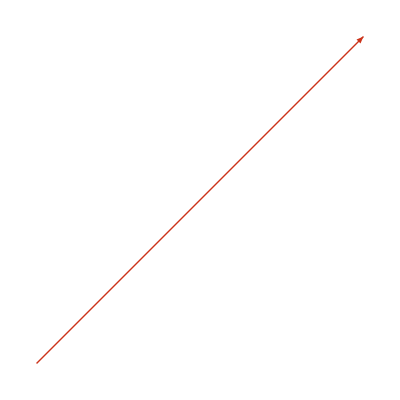

```mathematica
Graphics[{Blend[{Brown,Red},0.5],Arrow[{{{0,0},{1,1}}}]}]
```

```mathematica
subList[[1,1,1]]
```

Part::partd: Part specification subList⟦1,1,1⟧ is longer than depth of object.

subList⟦1,1,1⟧

### Equilibrium distribution plot

```mathematica
populationEqPlot[rho_,ux_,uy_,plotSize_]:=Module[{scale,arrowCollor,directions,directionLabels,populations,directionArrows},
scale = 0.7;
arrowCollor = Red;
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
directionLabels ={"f1","f2","f3","f4","f5","f6","f7","f8"};
directionLabels =Text[Style[#[[1]],Bold,Blue,FontSize->16],1.1#[[2]]]&/@Transpose@{directionLabels, scale*directions};
populations = feq[rho,ux,uy];
directionArrows=Graphics[{directionLabels,Thickness[0.004],Arrow[{{0,0}, scale*#}]& /@directions}];
Show[directionArrows,populationArrows[populations,plotSize]]
];
```

```mathematica
ShowEquilibriumPlot[]:=(Manipulate[populationEqPlot[rho,ux,uy,Tiny],{{rho,1.25, Style["Density (rho)",Bold]}, 0,2.5},{{ux,0, Style["Velocity in x-direction (ux)",Bold]},-0.5,0.5},{{uy,0,Style["Velocity in y-direction (uy)",Bold]},-0.5,0.5},FrameLabel->{"","",Style["Equilibrium distribution as functions of macroscapic values\n",Bold,Large,Purple]}]);
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

## Show Plot

```mathematica
ShowEquilibriumPlot[]
```

Actual  simulation

#### Clear all symbols

```mathematica
ClearAll[filename,populationList, subList,showSimulationGrid];
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

#### Get data from C++ simulation

```mathematica
SetDirectory[NotebookDirectory[]];
filename="population"<>".txt";
populationList = If[FileExistsQ[filename],Get[filename]];
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

#### Prepare data for presentation

```mathematica
(*subList = populationList[[All,3;;-3,3;;-3,;;-2]];*)
subList = populationList[[All,2;;-2,2;;-2,;;-2]];
(*subList = populationList[[All,1;;-1,1;;-1,;;-2]];*)
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
showSimulationGrid[]:=(ListAnimate[Grid[#,Frame->All]&/@Map[populationArrows[#,Tiny]&,subList,{3}],AnimationRunning->False,FrameLabel->{"","",Row[{Style["\n\tVelocity distributions for a real simulation\t\n",Bold,Large,Purple],Style["\n\t\t-Longer/wider arrows -> higher density (in that direction)\n\n",Bold,FontSize->16]}]}]);
```

#### Presentation

```mathematica
showSimulationGrid[]
```

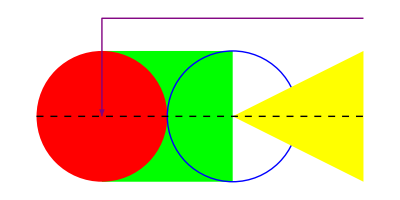

```mathematica
Graphics[{Thick, Green, Rectangle[{0, -1}, {2, 1}], Red, Disk[], Blue, Circle[{2, 0}], Yellow, Polygon[{{2, 0}, {4, 1}, {4, -1}}], Purple, Arrowheads[Large], Arrow[{{4, 3/2}, {0, 3/2}, {0, 0}}], Black, Dashed, Line[{{-1, 0}, {4, 0}}]}]
```



```mathematica
Graphics[{Red,Disk[{1,1},1]}]
```